# Crime Concentration Figure

## Parameters

```mathematica
TextSize=20;
```

```mathematica
TicksSize=15;
```

```mathematica
GraphThickness=0.01;
```

```mathematica
LinesThickness=0.007;
```

```mathematica
ColorsDiscrete=ResourceFunction["HexToColor"]/@{"#e3f4dd","#e2f4dd","#e2f4dc","#e1f3db","#e0f3db","#e0f3da","#dff3d9","#def2d9","#def2d8","#ddf2d7","#dcf2d7","#dcf1d6","#dbf1d5","#daf1d5","#daf0d4","#d9f0d3","#d8f0d3","#d8f0d2","#d7efd1","#d6efd1","#d6efd0","#d5efcf","#d4eecf","#d3eece","#d3eecd","#d2edcd","#d1edcc","#d0edcb","#d0edcb","#cfecca","#ceecca","#cdecc9","#cdebc8","#ccebc8","#cbebc7","#caeac6","#c9eac6","#c8eac5","#c7e9c5","#c6e9c4","#c5e8c4","#c5e8c3","#c4e8c2","#c3e7c2","#c2e7c1","#c1e7c1","#c0e6c0","#bfe6c0","#bde5bf","#bce5bf","#bbe5be","#bae4be","#b9e4be","#b8e3bd","#b7e3bd","#b6e2bd","#b5e2bc","#b3e1bc","#b2e1bc","#b1e1bb","#b0e0bb","#afe0bb","#aedfbb","#acdfbb","#abdeba","#aadeba","#a9ddba","#a7ddba","#a6dcba","#a5dcba","#a3dbba","#a2dbba","#a1daba","#a0daba","#9ed9bb","#9dd9bb","#9cd8bb","#9ad8bb","#99d7bb","#98d7bc","#96d6bc","#95d6bc","#93d5bd","#92d5bd","#91d4bd","#8fd3be","#8ed3be","#8dd2be","#8bd2bf","#8ad1bf","#88d1c0","#87d0c0","#86cfc1","#84cfc1","#83cec1","#81cec2","#80cdc2","#7fccc3","#7dccc3","#7ccbc4","#7acac4","#79cac5","#77c9c5","#76c8c6","#75c8c6","#73c7c7","#72c6c7","#70c5c7","#6fc5c8","#6ec4c8","#6cc3c9","#6bc3c9","#69c2ca","#68c1ca","#67c0ca","#65bfcb","#64bfcb","#63becb","#61bdcc","#60bccc","#5fbbcc","#5dbacc","#5cb9cc","#5ab9cd","#59b8cd","#58b7cd","#57b6cd","#55b5cd","#54b4cd","#53b3cd","#51b2cd","#50b1cd","#4fb0cd","#4eafcd","#4caecd","#4badcc","#4aaccc","#49abcc","#48aacc","#46a9cb","#45a8cb","#44a6cb","#43a5ca","#42a4ca","#41a3c9","#3fa2c9","#3ea1c8","#3da0c8","#3c9ec7","#3b9dc7","#3a9cc6","#399bc6","#379ac5","#3699c5","#3597c4","#3496c4","#3395c3","#3294c2","#3193c2","#3092c1","#2f90c0","#2d8fc0","#2c8ebf","#2b8dbf","#2a8cbe","#298abd","#2889bd","#2788bc","#2687bc","#2586bb","#2485ba","#2383ba","#2282b9","#2081b9","#1f80b8","#1e7fb7","#1d7eb7","#1c7db6","#1b7bb5","#1a7ab5","#1979b4","#1978b3","#1877b3","#1776b2","#1674b1","#1573b0","#1472b0","#1371af","#1370ae","#126fad","#116dac","#106cac","#106bab","#0f6aaa","#0e69a9","#0e67a8","#0d66a7","#0d65a6","#0c64a5","#0c63a4"}
```

{RGBColor[0.8901960784313725, 0.9568627450980391, 0.8666666666666667],RGBColor[0.8862745098039215, 0.9568627450980391, 0.8666666666666667],RGBColor[0.8862745098039215, 0.9568627450980391, 0.8627450980392157],RGBColor[0.8823529411764706, 0.9529411764705882, 0.8588235294117647],RGBColor[0.8784313725490196, 0.9529411764705882, 0.8588235294117647],RGBColor[0.8784313725490196, 0.9529411764705882, 0.8549019607843137],RGBColor[0.8745098039215686, 0.9529411764705882, 0.8509803921568627],RGBColor[0.8705882352941177, 0.9490196078431372, 0.8509803921568627],RGBColor[0.8705882352941177, 0.9490196078431372, 0.8470588235294118],RGBColor[0.8666666666666667, 0.9490196078431372, 0.8431372549019608],RGBColor[0.8627450980392157, 0.9490196078431372, 0.8431372549019608],RGBColor[0.8627450980392157, 0.9450980392156862, 0.8392156862745098],RGBColor[0.8588235294117647, 0.9450980392156862, 0.8352941176470589],RGBColor[0.8549019607843137, 0.9450980392156862, 0.8352941176470589],RGBColor[0.8549019607843137, 0.9411764705882353, 0.8313725490196078],RGBColor[0.8509803921568627, 0.9411764705882353, 0.8274509803921568],RGBColor[0.8470588235294118, 0.9411764705882353, 0.8274509803921568],RGBColor[0.8470588235294118, 0.9411764705882353, 0.8235294117647058],RGBColor[0.8431372549019608, 0.9372549019607843, 0.8196078431372549],RGBColor[0.8392156862745098, 0.9372549019607843, 0.8196078431372549],RGBColor[0.8392156862745098, 0.9372549019607843, 0.8156862745098039],RGBColor[0.8352941176470589, 0.9372549019607843, 0.8117647058823529],RGBColor[0.8313725490196078, 0.9333333333333333, 0.8117647058823529],RGBColor[0.8274509803921568, 0.9333333333333333, 0.807843137254902],RGBColor[0.8274509803921568, 0.9333333333333333, 0.803921568627451],RGBColor[0.8235294117647058, 0.9294117647058824, 0.803921568627451],RGBColor[0.8196078431372549, 0.9294117647058824, 0.8],RGBColor[0.8156862745098039, 0.9294117647058824, 0.796078431372549],RGBColor[0.8156862745098039, 0.9294117647058824, 0.796078431372549],RGBColor[0.8117647058823529, 0.9254901960784314, 0.792156862745098],RGBColor[0.807843137254902, 0.9254901960784314, 0.792156862745098],RGBColor[0.803921568627451, 0.9254901960784314, 0.788235294117647],RGBColor[0.803921568627451, 0.9215686274509803, 0.7843137254901961],RGBColor[0.8, 0.9215686274509803, 0.7843137254901961],RGBColor[0.796078431372549, 0.9215686274509803, 0.7803921568627451],RGBColor[0.792156862745098, 0.9176470588235294, 0.7764705882352941],RGBColor[0.788235294117647, 0.9176470588235294, 0.7764705882352941],RGBColor[0.7843137254901961, 0.9176470588235294, 0.7725490196078432],RGBColor[0.7803921568627451, 0.9137254901960784, 0.7725490196078432],RGBColor[0.7764705882352941, 0.9137254901960784, 0.7686274509803921],RGBColor[0.7725490196078432, 0.9098039215686274, 0.7686274509803921],RGBColor[0.7725490196078432, 0.9098039215686274, 0.7647058823529411],RGBColor[0.7686274509803921, 0.9098039215686274, 0.7607843137254902],RGBColor[0.7647058823529411, 0.9058823529411765, 0.7607843137254902],RGBColor[0.7607843137254902, 0.9058823529411765, 0.7568627450980392],RGBColor[0.7568627450980392, 0.9058823529411765, 0.7568627450980392],RGBColor[0.7529411764705882, 0.9019607843137255, 0.7529411764705882],RGBColor[0.7490196078431373, 0.9019607843137255, 0.7529411764705882],RGBColor[0.7411764705882353, 0.8980392156862745, 0.7490196078431373],RGBColor[0.7372549019607844, 0.8980392156862745, 0.7490196078431373],RGBColor[0.7333333333333333, 0.8980392156862745, 0.7450980392156863],RGBColor[0.7294117647058823, 0.8941176470588235, 0.7450980392156863],RGBColor[0.7254901960784313, 0.8941176470588235, 0.7450980392156863],RGBColor[0.7215686274509804, 0.8901960784313725, 0.7411764705882353],RGBColor[0.7176470588235294, 0.8901960784313725, 0.7411764705882353],RGBColor[0.7137254901960784, 0.8862745098039215, 0.7411764705882353],RGBColor[0.7098039215686275, 0.8862745098039215, 0.7372549019607844],RGBColor[0.7019607843137254, 0.8823529411764706, 0.7372549019607844],RGBColor[0.6980392156862745, 0.8823529411764706, 0.7372549019607844],RGBColor[0.6941176470588235, 0.8823529411764706, 0.7333333333333333],RGBColor[0.6901960784313725, 0.8784313725490196, 0.7333333333333333],RGBColor[0.6862745098039216, 0.8784313725490196, 0.7333333333333333],RGBColor[0.6823529411764706, 0.8745098039215686, 0.7333333333333333],RGBColor[0.6745098039215687, 0.8745098039215686, 0.7333333333333333],RGBColor[0.6705882352941176, 0.8705882352941177, 0.7294117647058823],RGBColor[0.6666666666666666, 0.8705882352941177, 0.7294117647058823],RGBColor[0.6627450980392157, 0.8666666666666667, 0.7294117647058823],RGBColor[0.6549019607843137, 0.8666666666666667, 0.7294117647058823],RGBColor[0.6509803921568628, 0.8627450980392157, 0.7294117647058823],RGBColor[0.6470588235294118, 0.8627450980392157, 0.7294117647058823],RGBColor[0.6392156862745098, 0.8588235294117647, 0.7294117647058823],RGBColor[0.6352941176470588, 0.8588235294117647, 0.7294117647058823],RGBColor[0.6313725490196078, 0.8549019607843137, 0.7294117647058823],RGBColor[0.6274509803921569, 0.8549019607843137, 0.7294117647058823],RGBColor[0.6196078431372549, 0.8509803921568627, 0.7333333333333333],RGBColor[0.615686274509804, 0.8509803921568627, 0.7333333333333333],RGBColor[0.611764705882353, 0.8470588235294118, 0.7333333333333333],RGBColor[0.6039215686274509, 0.8470588235294118, 0.7333333333333333],RGBColor[0.6, 0.8431372549019608, 0.7333333333333333],RGBColor[0.596078431372549, 0.8431372549019608, 0.7372549019607844],RGBColor[0.5882352941176471, 0.8392156862745098, 0.7372549019607844],RGBColor[0.5843137254901961, 0.8392156862745098, 0.7372549019607844],RGBColor[0.5764705882352941, 0.8352941176470589, 0.7411764705882353],RGBColor[0.5725490196078431, 0.8352941176470589, 0.7411764705882353],RGBColor[0.5686274509803921, 0.8313725490196078, 0.7411764705882353],RGBColor[0.5607843137254902, 0.8274509803921568, 0.7450980392156863],RGBColor[0.5568627450980392, 0.8274509803921568, 0.7450980392156863],RGBColor[0.5529411764705883, 0.8235294117647058, 0.7450980392156863],RGBColor[0.5450980392156862, 0.8235294117647058, 0.7490196078431373],RGBColor[0.5411764705882353, 0.8196078431372549, 0.7490196078431373],RGBColor[0.5333333333333333, 0.8196078431372549, 0.7529411764705882],RGBColor[0.5294117647058824, 0.8156862745098039, 0.7529411764705882],RGBColor[0.5254901960784314, 0.8117647058823529, 0.7568627450980392],RGBColor[0.5176470588235293, 0.8117647058823529, 0.7568627450980392],RGBColor[0.5137254901960784, 0.807843137254902, 0.7568627450980392],RGBColor[0.5058823529411764, 0.807843137254902, 0.7607843137254902],RGBColor[0.5019607843137255, 0.803921568627451, 0.7607843137254902],RGBColor[0.4980392156862745, 0.8, 0.7647058823529411],RGBColor[0.49019607843137253, 0.8, 0.7647058823529411],RGBColor[0.48627450980392156, 0.796078431372549, 0.7686274509803921],RGBColor[0.4784313725490196, 0.792156862745098, 0.7686274509803921],RGBColor[0.4745098039215686, 0.792156862745098, 0.7725490196078432],RGBColor[0.4666666666666667, 0.788235294117647, 0.7725490196078432],RGBColor[0.4627450980392157, 0.7843137254901961, 0.7764705882352941],RGBColor[0.4588235294117647, 0.7843137254901961, 0.7764705882352941],RGBColor[0.45098039215686275, 0.7803921568627451, 0.7803921568627451],RGBColor[0.44705882352941173, 0.7764705882352941, 0.7803921568627451],RGBColor[0.4392156862745098, 0.7725490196078432, 0.7803921568627451],RGBColor[0.43529411764705883, 0.7725490196078432, 0.7843137254901961],RGBColor[0.43137254901960786, 0.7686274509803921, 0.7843137254901961],RGBColor[0.4235294117647059, 0.7647058823529411, 0.788235294117647],RGBColor[0.4196078431372549, 0.7647058823529411, 0.788235294117647],RGBColor[0.4117647058823529, 0.7607843137254902, 0.792156862745098],RGBColor[0.40784313725490196, 0.7568627450980392, 0.792156862745098],RGBColor[0.403921568627451, 0.7529411764705882, 0.792156862745098],RGBColor[0.396078431372549, 0.7490196078431373, 0.796078431372549],RGBColor[0.39215686274509803, 0.7490196078431373, 0.796078431372549],RGBColor[0.38823529411764707, 0.7450980392156863, 0.796078431372549],RGBColor[0.3803921568627451, 0.7411764705882353, 0.8],RGBColor[0.3764705882352941, 0.7372549019607844, 0.8],RGBColor[0.37254901960784315, 0.7333333333333333, 0.8],RGBColor[0.36470588235294116, 0.7294117647058823, 0.8],RGBColor[0.3607843137254902, 0.7254901960784313, 0.8],RGBColor[0.3529411764705882, 0.7254901960784313, 0.803921568627451],RGBColor[0.34901960784313724, 0.7215686274509804, 0.803921568627451],RGBColor[0.34509803921568627, 0.7176470588235294, 0.803921568627451],RGBColor[0.3411764705882353, 0.7137254901960784, 0.803921568627451],RGBColor[0.3333333333333333, 0.7098039215686275, 0.803921568627451],RGBColor[0.32941176470588235, 0.7058823529411764, 0.803921568627451],RGBColor[0.3254901960784314, 0.7019607843137254, 0.803921568627451],RGBColor[0.3176470588235294, 0.6980392156862745, 0.803921568627451],RGBColor[0.3137254901960784, 0.6941176470588235, 0.803921568627451],RGBColor[0.30980392156862746, 0.6901960784313725, 0.803921568627451],RGBColor[0.3058823529411765, 0.6862745098039216, 0.803921568627451],RGBColor[0.2980392156862745, 0.6823529411764706, 0.803921568627451],RGBColor[0.29411764705882354, 0.6784313725490196, 0.8],RGBColor[0.2901960784313725, 0.6745098039215687, 0.8],RGBColor[0.28627450980392155, 0.6705882352941176, 0.8],RGBColor[0.2823529411764706, 0.6666666666666666, 0.8],RGBColor[0.27450980392156865, 0.6627450980392157, 0.796078431372549],RGBColor[0.27058823529411763, 0.6588235294117647, 0.796078431372549],RGBColor[0.26666666666666666, 0.6509803921568628, 0.796078431372549],RGBColor[0.2627450980392157, 0.6470588235294118, 0.792156862745098],RGBColor[0.2588235294117647, 0.6431372549019607, 0.792156862745098],RGBColor[0.2549019607843137, 0.6392156862745098, 0.788235294117647],RGBColor[0.24705882352941178, 0.6352941176470588, 0.788235294117647],RGBColor[0.24313725490196078, 0.6313725490196078, 0.7843137254901961],RGBColor[0.2392156862745098, 0.6274509803921569, 0.7843137254901961],RGBColor[0.23529411764705882, 0.6196078431372549, 0.7803921568627451],RGBColor[0.23137254901960785, 0.615686274509804, 0.7803921568627451],RGBColor[0.22745098039215686, 0.611764705882353, 0.7764705882352941],RGBColor[0.22352941176470587, 0.6078431372549019, 0.7764705882352941],RGBColor[0.21568627450980393, 0.6039215686274509, 0.7725490196078432],RGBColor[0.21176470588235294, 0.6, 0.7725490196078432],RGBColor[0.20784313725490194, 0.592156862745098, 0.7686274509803921],RGBColor[0.20392156862745098, 0.5882352941176471, 0.7686274509803921],RGBColor[0.2, 0.5843137254901961, 0.7647058823529411],RGBColor[0.19607843137254902, 0.580392156862745, 0.7607843137254902],RGBColor[0.19215686274509802, 0.5764705882352941, 0.7607843137254902],RGBColor[0.18823529411764706, 0.5725490196078431, 0.7568627450980392],RGBColor[0.1843137254901961, 0.5647058823529412, 0.7529411764705882],RGBColor[0.1764705882352941, 0.5607843137254902, 0.7529411764705882],RGBColor[0.17254901960784313, 0.5568627450980392, 0.7490196078431373],RGBColor[0.16862745098039217, 0.5529411764705883, 0.7490196078431373],RGBColor[0.16470588235294117, 0.5490196078431373, 0.7450980392156863],RGBColor[0.16078431372549018, 0.5411764705882353, 0.7411764705882353],RGBColor[0.1568627450980392, 0.5372549019607843, 0.7411764705882353],RGBColor[0.15294117647058825, 0.5333333333333333, 0.7372549019607844],RGBColor[0.14901960784313725, 0.5294117647058824, 0.7372549019607844],RGBColor[0.14509803921568626, 0.5254901960784314, 0.7333333333333333],RGBColor[0.1411764705882353, 0.5215686274509804, 0.7294117647058823],RGBColor[0.13725490196078433, 0.5137254901960784, 0.7294117647058823],RGBColor[0.13333333333333333, 0.5098039215686274, 0.7254901960784313],RGBColor[0.12549019607843137, 0.5058823529411764, 0.7254901960784313],RGBColor[0.12156862745098039, 0.5019607843137255, 0.7215686274509804],RGBColor[0.11764705882352941, 0.4980392156862745, 0.7176470588235294],RGBColor[0.11372549019607843, 0.49411764705882355, 0.7176470588235294],RGBColor[0.10980392156862745, 0.49019607843137253, 0.7137254901960784],RGBColor[0.10588235294117647, 0.4823529411764706, 0.7098039215686275],RGBColor[0.10196078431372549, 0.4784313725490196, 0.7098039215686275],RGBColor[0.09803921568627451, 0.4745098039215686, 0.7058823529411764],RGBColor[0.09803921568627451, 0.47058823529411764, 0.7019607843137254],RGBColor[0.09411764705882353, 0.4666666666666667, 0.7019607843137254],RGBColor[0.09019607843137255, 0.4627450980392157, 0.6980392156862745],RGBColor[0.08627450980392157, 0.4549019607843137, 0.6941176470588235],RGBColor[0.08235294117647059, 0.45098039215686275, 0.6901960784313725],RGBColor[0.0784313725490196, 0.44705882352941173, 0.6901960784313725],RGBColor[0.07450980392156863, 0.44313725490196076, 0.6862745098039216],RGBColor[0.07450980392156863, 0.4392156862745098, 0.6823529411764706],RGBColor[0.07058823529411765, 0.43529411764705883, 0.6784313725490196],RGBColor[0.06666666666666667, 0.42745098039215684, 0.6745098039215687],RGBColor[0.06274509803921569, 0.4235294117647059, 0.6745098039215687],RGBColor[0.06274509803921569, 0.4196078431372549, 0.6705882352941176],RGBColor[0.058823529411764705, 0.4156862745098039, 0.6666666666666666],RGBColor[0.054901960784313725, 0.4117647058823529, 0.6627450980392157],RGBColor[0.054901960784313725, 0.403921568627451, 0.6588235294117647],RGBColor[0.050980392156862744, 0.4, 0.6549019607843137],RGBColor[0.050980392156862744, 0.396078431372549, 0.6509803921568628],RGBColor[0.047058823529411764, 0.39215686274509803, 0.6470588235294118],RGBColor[0.047058823529411764, 0.38823529411764707, 0.6431372549019607]}

```mathematica
ColorGradient=Blend[ColorsDiscrete,#]&
```

Blend[ColorsDiscrete,#1]&

```mathematica
color1=RGBColor[0.047058823529411764,0.38823529411764707,0.6431372549019607]
```

RGBColor[0.047058823529411764, 0.38823529411764707, 0.6431372549019607]

```mathematica
color2=RGBColor[0.5769319492502883,0.8355247981545559,0.7409457900807382]
```

RGBColor[0.5769319492502883, 0.8355247981545559, 0.7409457900807382]

## Boston

## Load the Data

```mathematica
CrimeList={"Property_Crime","Violent_Crime"}
```

{Property_Crime,Violent_Crime}

```mathematica
YearsList=Range[2015,2024]
```

{2015,2016,2017,2018,2019,2020,2021,2022,2023,2024}

```mathematica
colors=ColorGradient/@Rescale[Range[Length[YearsList]]]
```

{RGBColor[0.8901960784313725, 0.9568627450980391, 0.8666666666666667],RGBColor[0.8309368191721133, 0.9333333333333333, 0.8113289760348584],RGBColor[0.759912854030501, 0.9058823529411765, 0.7568627450980392],RGBColor[0.6601307189542484, 0.8666666666666667, 0.7294117647058823],RGBColor[0.543355119825708, 0.8217864923747277, 0.7490196078431373],RGBColor[0.42135076252723314, 0.7647058823529411, 0.788235294117647],RGBColor[0.30718954248366015, 0.6875816993464052, 0.803921568627451],RGBColor[0.2047930283224401, 0.5891067538126362, 0.7686274509803921],RGBColor[0.110239651416122, 0.4906318082788671, 0.714161220043573],RGBColor[0.047058823529411764, 0.38823529411764707, 0.6431372549019607]}

```mathematica
City="Boston"
```

Boston

### Lorenz Curves

```mathematica
SetDirectory["..."]
```

```mathematica
BostonLorenzNames={};
```

```mathematica
Do[blockFile="Lorenz_Block_Share_"<>crime<>"_Year_"<>ToString[year]<>"_"<>City<>".mat";
crimeFile="Lorenz_Crime_Share_"<>crime<>"_Year_"<>ToString[year]<>"_"<>City<>".mat";
blockData=Flatten@Import[blockFile];
crimeData=Flatten@Import[crimeFile];
data=Partition[Riffle[blockData,crimeData],2];
cleanCrime=StringReplace[crime,"_"->""];
varNameString=City<>cleanCrime<>ToString[year];
ToExpression[varNameString<>" = data"];
AppendTo[BostonLorenzNames,varNameString];,{crime,CrimeList},{year,YearsList}]
```

```mathematica
BostonLorenzNames
```

{BostonPropertyCrime2015,BostonPropertyCrime2016,BostonPropertyCrime2017,BostonPropertyCrime2018,BostonPropertyCrime2019,BostonPropertyCrime2020,BostonPropertyCrime2021,BostonPropertyCrime2022,BostonPropertyCrime2023,BostonPropertyCrime2024,BostonViolentCrime2015,BostonViolentCrime2016,BostonViolentCrime2017,BostonViolentCrime2018,BostonViolentCrime2019,BostonViolentCrime2020,BostonViolentCrime2021,BostonViolentCrime2022,BostonViolentCrime2023,BostonViolentCrime2024}

```mathematica
Length[BostonLorenzNames]
```

20

```mathematica
BostonLorenzProperty=BostonLorenzNames[[1;;Length[BostonLorenzNames]/2]]
```

{BostonPropertyCrime2015,BostonPropertyCrime2016,BostonPropertyCrime2017,BostonPropertyCrime2018,BostonPropertyCrime2019,BostonPropertyCrime2020,BostonPropertyCrime2021,BostonPropertyCrime2022,BostonPropertyCrime2023,BostonPropertyCrime2024}

```mathematica
BostonLorenzViolent=BostonLorenzNames[[(Length[BostonLorenzNames]/2+1);;-1]]
```

{BostonViolentCrime2015,BostonViolentCrime2016,BostonViolentCrime2017,BostonViolentCrime2018,BostonViolentCrime2019,BostonViolentCrime2020,BostonViolentCrime2021,BostonViolentCrime2022,BostonViolentCrime2023,BostonViolentCrime2024}

### Annual Crimes

```mathematica
SetDirectory["..."]
```

```mathematica
BostonAnnualRatesNames={};
```

```mathematica
Do[cleanCrime=StringReplace[crime,"_"->""];
varNameStr=City<>cleanCrime<>"AnnualRates";
dataList=Table[fileName="Total_Crime_"<>crime<>"_Year_"<>ToString[year]<>"_"<>City<>".mat";
rawData=Import[fileName];
First@Flatten[rawData],{year,YearsList}];
ToExpression[varNameStr<>" = dataList"];
AppendTo[BostonAnnualRatesNames,varNameStr];,{crime,CrimeList}]
```

```mathematica
BostonAnnualRatesNames
```

{BostonPropertyCrimeAnnualRates,BostonViolentCrimeAnnualRates}

```mathematica
BostonPropertyCrimeAnnualRates=Partition[Riffle[YearsList,BostonPropertyCrimeAnnualRates],2]
```

{{2015,9689.},{2016,14650.},{2017,13948.},{2018,13749.},{2019,13041.},{2020,12001.},{2021,10443.},{2022,10143.},{2023,11255.},{2024,11887.}}

```mathematica
{Min[BostonPropertyCrimeAnnualRates[[All,2]]],Max[BostonPropertyCrimeAnnualRates[[All,2]]]}
```

{9689.,14650.}

```mathematica
BostonViolentCrimeAnnualRates=Partition[Riffle[YearsList,BostonViolentCrimeAnnualRates],2]
```

{{2015,2268.},{2016,3642.},{2017,3582.},{2018,3453.},{2019,3159.},{2020,2560.},{2021,2166.},{2022,2214.},{2023,2252.},{2024,2336.}}

```mathematica
{Min[BostonViolentCrimeAnnualRates[[All,2]]],Max[BostonViolentCrimeAnnualRates[[All,2]]]}
```

{2166.,3642.}

## Get Crime Concentration

```mathematica
BostonCrimeConcentrationsProperty50=Partition[Riffle[YearsList,Table[Module[{interp,xVal},interp=Interpolation[ToExpression[BostonLorenzProperty[[i]]]];
xVal=x/. FindRoot[interp[x]==0.5,{x,0.9,1}];xVal=(1-xVal)*100;
xVal],{i,Length[BostonLorenzProperty]}]],2]
```

{{2015,7.47719},{2016,7.01673},{2017,6.85801},{2018,6.54299},{2019,5.0302},{2020,0.994473},{2021,0.888478},{2022,0.805552},{2023,0.589121},{2024,0.463023}}

```mathematica
{Min[BostonCrimeConcentrationsProperty50[[All,2]]],Max[BostonCrimeConcentrationsProperty50[[All,2]]]}
```

{0.463023,7.47719}

```mathematica
BostonCrimeConcentrationsProperty25=Partition[Riffle[YearsList,Table[Module[{interp,xVal},interp=Interpolation[ToExpression[BostonLorenzProperty[[i]]]];
xVal=x/. FindRoot[interp[x]==0.75,{x,0.9,1}];xVal=(1-xVal)*100;
xVal],{i,Length[BostonLorenzProperty]}]],2]
```

{{2015,1.81825},{2016,1.58793},{2017,1.39574},{2018,1.34477},{2019,0.752049},{2020,0.0937956},{2021,0.118803},{2022,0.109241},{2023,0.105316},{2024,0.115012}}

```mathematica
{Min[BostonCrimeConcentrationsProperty25[[All,2]]],Max[BostonCrimeConcentrationsProperty25[[All,2]]]}
```

{0.0937956,1.81825}

```mathematica
BostonCrimeConcentrationsViolent50=Partition[Riffle[YearsList,Table[Module[{interp,xVal},interp=Interpolation[ToExpression[BostonLorenzViolent[[i]]]];
xVal=x/. FindRoot[interp[x]==0.5,{x,0.9,1}];xVal=(1-xVal)*100;
xVal],{i,Length[BostonLorenzViolent]}]],2]
```

{{2015,4.41027},{2016,5.37907},{2017,5.1763},{2018,4.74189},{2019,4.66092},{2020,3.63862},{2021,2.95145},{2022,3.17112},{2023,3.05847},{2024,3.3063}}

```mathematica
{Min[BostonCrimeConcentrationsViolent50[[All,2]]],Max[BostonCrimeConcentrationsViolent50[[All,2]]]}
```

{2.95145,5.37907}

```mathematica
BostonCrimeConcentrationsViolent25=Partition[Riffle[YearsList,Table[Module[{interp,xVal},interp=Interpolation[ToExpression[BostonLorenzViolent[[i]]]];
xVal=x/. FindRoot[interp[x]==0.75,{x,0.9,1}];xVal=(1-xVal)*100;
xVal],{i,Length[BostonLorenzViolent]}]],2]
```

{{2015,1.43207},{2016,1.75031},{2017,1.59542},{2018,1.56655},{2019,1.41588},{2020,0.827982},{2021,0.674697},{2022,0.708291},{2023,0.695216},{2024,0.816545}}

```mathematica
{Min[BostonCrimeConcentrationsViolent25[[All,2]]],Max[BostonCrimeConcentrationsViolent25[[All,2]]]}
```

{0.674697,1.75031}

## Plotting

```mathematica
labelsRates={"Property Crime","Violent Crime"};
labelsConcentration={"Property 50%","Violent 50%","Property 25%","Violent 25%"};
```

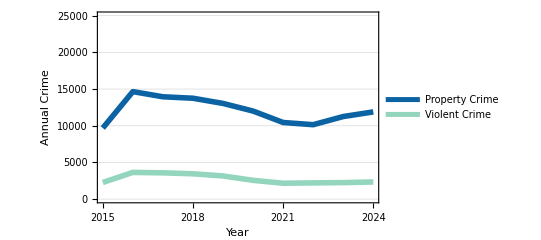

```mathematica
BostonAnnualRatePlot=ListLinePlot[{BostonPropertyCrimeAnnualRates,BostonViolentCrimeAnnualRates},PlotRange->{{Min[YearsList],Max[YearsList]},{0,25000}},PlotStyle->{{color1,Thickness[GraphThickness]},{color2,Thickness[GraphThickness]}},Frame->True,AspectRatio->0.6,GridLines->Automatic,FrameLabel->{Style["Year",TextSize,FontFamily->"Arial"],Style["Annual Crime",TextSize,FontFamily->"Arial"]},FrameTicks->{{Automatic,None},{{2015,2018,2021,2024},None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],PlotLegends->Placed[LineLegend[labelsRates],{0.35,0.825}],ImageSize->{Automatic,250}]
```

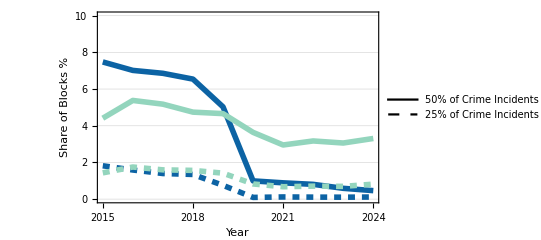

```mathematica
b=ListLinePlot[{BostonCrimeConcentrationsProperty50,BostonCrimeConcentrationsViolent50,BostonCrimeConcentrationsProperty25,BostonCrimeConcentrationsViolent25},PlotRange->{{Min[YearsList],Max[YearsList]},{0,10}},PlotStyle->{{color1,Thickness[GraphThickness]},{color2,Thickness[GraphThickness]},{Dashed,color1,Thickness[GraphThickness]},{Dashed,color2,Thickness[GraphThickness]}},GridLines->Automatic,Frame->True,AspectRatio->0.6,FrameLabel->{Style["Year",TextSize,FontFamily->"Arial"],Style["Share of Blocks %",TextSize,FontFamily->"Arial"]},FrameTicks->{{Automatic,None},{{2015,2018,2021,2024},None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],PlotLegends->Placed[LineLegend[{Directive[Black],Directive[Black,Dashed]},{"50% of Crime Incidents","25% of Crime Incidents"}],{0.45,0.825}],ImageSize->{Automatic,250}]
```